# Collecting, Visualizing, and Analyzing Egyptian Pyramids Data

Ahmed Elbanna

## Introduction

There are several ancient pyramids in the world built by different civilizations. Egyptian pyramids captured the attention of many people around the world for many years due to its size and design. The most famous ones are the three largest ones in Egypt located in Giza-Cairo; however, there are other pyramids in Egypt even some with notable size.
	In this article I am going to collect the data needed about the pyramids in Egypt, show two ways available to store and deal with the data, then I will visualize some relations extracted from the data. Finally I will try to answer some interesting questions using statistical hypothesis .

## Collecting Data

First, Wolfram language contains some information about the pyramids stored as Entities, but it has some missing values in them so I decided to just collect them from Wikipedia pages, which was not very quick but it did the job.
Wikipedia has a page that talks about the Egyptian pyramids in general, then a dedicated page for each one of them. I will collect the names of the available pyramids from the general page first .

```mathematica
raw=Import["https://en.wikipedia.org/wiki/Egyptian_pyramids","Source"];
pynamesraw=StringCases[raw,"<table class=\"wikitable\">"~~Shortest[x__]~~"</td></tr></tbody></table>"->x];
pynamesraw=First@StringCases[pynamesraw,"\"/wiki/"~~Shortest[x__]~~"\" "->x]
```

{Djoser,Saqqara,Sneferu,Dashur,Sneferu,Meidum,Cubits,Khufu,Giza_pyramid_complex,Cubits,Djedefre,Abu_Rawash,Khafre,Giza_pyramid_complex,Cubits,Menkaure,Giza_pyramid_complex,Cubits,Userkaf,Saqqara,Sahure,Abusir,Neferirkare_Kakai,Abusir,Nyuserre_Ini,Abusir,Cubits,Amenemhat_I,Lisht,Senusret_I,Lisht,Senusret_II,El-Lahun,Cubits,Cubits,Amenemhat_III,Hawara,Khendjer,Saqqara,Piye,El-Kurru,Taharqa,Nuri}

By inspecting the output, it turns out that I actually imported the names and locations together alternating with each other {Name,Location,Name,..etc}. Also the list contains the unit “Cubits” which appear in some comments in the table I am importing and I am going to remove the pyramid “Djedefre” as it was never completed, and Piye’s pyramid since I couldn’t find info about it .

```mathematica
pynamesraw=Drop[pynamesraw,{11,12}];
pynamesraw=Drop[pynamesraw,{-4,-3}];pynamesraw=Drop[pynamesraw,{-2,-1}];
pynamesraw=DeleteCases[pynamesraw,"Cubits"];
```

Let us separate the names from locations. Pyramids are usually named after its King/pharaoh so we will take the Kings’ names as the pyramids’ names.

```mathematica
pynames=pynamesraw⟦Range[1,Length@pynamesraw,2]⟧
```

{Djoser,Sneferu,Sneferu,Khufu,Khafre,Menkaure,Userkaf,Sahure,Neferirkare_Kakai,Nyuserre_Ini,Amenemhat_I,Senusret_I,Senusret_II,Amenemhat_III,Khendjer}

```mathematica
pylocations=pynamesraw⟦Range[2,Length@pynamesraw,2]⟧
```

{Saqqara,Dashur,Meidum,Giza_pyramid_complex,Giza_pyramid_complex,Giza_pyramid_complex,Saqqara,Abusir,Abusir,Abusir,Lisht,Lisht,El-Lahun,Hawara,Saqqara}

```mathematica
{Length@pynames,Length@pylocations}
```

{15,15}

Not just three pyramids right?! Let us explore each one and try to import its specific data. Starting with “Djoser”, I will search wikipedia for an article of the pyramid of Djoser.

```mathematica
StringCases[WikipediaSearch["Djoser"],___~~"Pyramid"~~___]
```

{{},{Djoser Step Pyramid},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

We have an article on Wikipedia called “Djoser Step Pyramid” which for sure has the information we need. We will import the source of that page and extract the information needed out of it. The page’s URL can be formed by adding the articles’ name to https://en.wikipedia.org/wiki/ .

```mathematica
djoserraw=Import["https://en.wikipedia.org/wiki/Djoser Step Pyramid","Source"];
```

Like before, we look at the source page and try to look for our data and extract it. Doing that for the 15 pyramids and collect the data in a file for further investigation. I stored it in an iconized shape as follows (added one more pyramid which wasn’t found in the general page)

```mathematica
data=;
data⟦1;;3⟧
```

{{name,image,position,height_m,base_m,year,slope_%},{Djoser,https://en.wikipedia.org/wiki/File:Saqqara_pyramid_ver_2.jpg,{29.8713,31.2164},62.5,121,2648,103},{Sneferu_bent,https://en.wikipedia.org/wiki/File:Snefru%27s_Bent_Pyramid_in_Dahshur.jpg,{29.7903,31.2092},104.74,189.61,2600,93}}

Just to speed up things I will remove the header

```mathematica
info=data⟦1⟧
```

{name,image,position,height_m,base_m,year,slope_%}

```mathematica
data=Rest@data;
```

## Visualization and Analysis

Which part of Egypt these pyramids were built in?
to answer that I will generate a disk on Egypt’s map with its center as the average of the pyramids’ locations, and radius as the maximum distance of pyramids’ pairs’s distances.

```mathematica
loc=data⟦All,3⟧;
GeoGraphics[GeoDisk[Mean@data⟦All,3⟧,Max@GeoDistanceList@loc],GeoRange->Entity["Country","Egypt"]]
```

-Graphics-

Let’s take a closer look, and also show the path between the pyramids, in case you want to take a tour around them.

```mathematica
GeoGraphics[{Blue,Thick,GeoMarker[loc,EntityClass["Polyhedron","Pyramid"]["Image"]⟦1⟧],GeoPath@loc⟦FindShortestTour[loc]⟦2⟧⟧}]
```

-Graphics-

Is there a relation between the height and building year of the pyramid?
First, I will look at the plot of these two parameters, then I will test the relation. My comment comes after that.

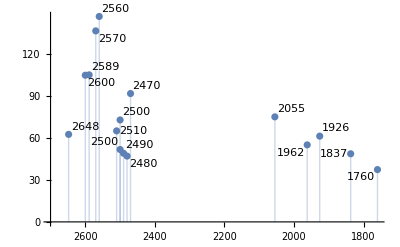

```mathematica
ListPlot[Table[Labeled[data⟦All,{6,4}⟧⟦i⟧,data⟦All,6⟧⟦i⟧],{i,Length@data}],Filling->Axis,ScalingFunctions->{"Reverse",Identity},AxesOrigin->{2700,0}]
```

```mathematica
CorrelationTest[data⟦All,{6,4}⟧,0,{"TestDataTable","TestConclusion"}]
```

{ | Statistic | P-Value
Spearman Rank | 0.637233 | 0.00659185,The null hypothesis that the population rank correlation coefficient is equal to 0. is rejected at the 5 percent level based on the Spearman Rank test.}

Now we have a statistical proof that the height and finishing year are correlated Negatively. From the plot it looks like building pyramids flourished from as early as 2648 BC till 2470 BC then there was a gap where no pyramids were built in Egypt, then started at short scale in 2055 BC declining to the minimum when  various armies conquered Egypt.
Actually the Wolfram language did quite well choosing the Spearman rank test as by looking at the data, it looks like it is not normally distributed.
During working on this article Riccardo Di Virgilio showed me how effective can working with the data be using Associations, so let us make the following section using them .

Since the largest pyramids are located in Cairo, I am wondering if pyramids gets smaller as we get far from Cairo?
To check that I will construct an association and test the correlation

```mathematica
data2=MapThread[Association][{Thread["pyramid"->data⟦All,1⟧],Thread["distance_to_cairo"->GeoDistance[CityData[Entity["City",{"Cairo","Cairo","Egypt"}],"Coordinates"],#]&/@data⟦All,3⟧],Thread["height"->data⟦All,4⟧],Thread["time"->data⟦All,6⟧],Thread["slope"->data⟦All,7⟧]}];
```

By that we have a dataset contains for each pyramid its name, distance to Cairo, ...,etc, let us have a look

```mathematica
Dataset[data2]
```

Dataset[<>]

```mathematica
CorrelationTest[Lookup[data2,{"height","distance_to_cairo"}],0,{"TestDataTable","TestConclusion"}]
```

{ | Statistic | P-Value
Spearman Rank | -0.2 | 0.464802,The null hypothesis that the population rank correlation coefficient is equal to 0. is not rejected at the 5 percent level based on the Spearman Rank test.}

Unfortunately there is no statistical evidence that height and distance to Cairo are correlated but let’s look at it any way

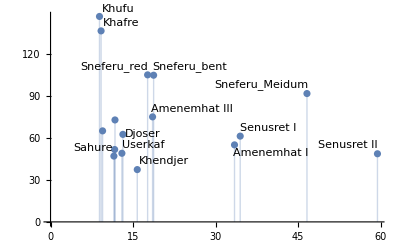

```mathematica
ListPlot[Table[Labeled[Lookup[data2,{"distance_to_cairo","height"}]⟦i⟧,Lookup[data2,"pyramid"]⟦i⟧],{i,Length@data}],Filling->Axis]
```

Assuming that the axis labels are known from the input, the plot shows that some pyramids such as Sahure, Djoser were early attempts and they simply didn’t have the tools to get higher.

### Contact:

```mathematica
Entity["InternetDomain","ahmed@math.bme.hu"]
```